Multidimensional scaling
-Need symmetric distance-like data

Treat each object as a vector in R^n
GOAL: Find the “best” vectors that describes our distance data
minimize the stress function - its a measure of the distance btween vectors & distances btween our data

stress -> f(x_1,...,x_k)=Sum[{i<j}, (d_(ij) - || x _i- x _j ||)^2
stress -> f(x_1,...,x_k)=Sum[{i<j}, (d_(1j) - || x _1- x _j ||)^2
															|| x _i- x _j || = Sqrt[(x_(i1)-x_(j1))^2+...+(x_(in)-x_(jn))^2]
deriv. of stress =Sum[{k,j=1}, 2(d_(1j) - || x _1- x _j ||)*(-1/2)(|| x _1- x _j ||)^(-1/2) * 2(x_(11)-x_(j1))]
deriv. of stress =Sum[{k,j=1},-2(d_(1j) - || x _1- x _j ||)*(|| x _1- x _j ||)^(-1/2) * (x_(11)-x_(j1))]
deriv. of stress =Sum[{k,j=1}, -2((d_(rj)/ || x _r- x _j ||)-1)* (x_(rL)-x_(jL))]

Multi Dimensional scaling - symmetric data dimensional reduction technique

```mathematica
candybars={"Snickers","Hershey’s","Kit Kat","Twix","3 Musketeers"," Milky Way Bar"}
Subsets[candybars,{2}]//Grid
```

{Snickers,Hershey’s,Kit Kat,Twix,3 Musketeers, Milky Way Bar}

Snickers | Hershey’s
Snickers | Kit Kat
Snickers | Twix
Snickers | 3 Musketeers
Snickers |  Milky Way Bar
Hershey’s | Kit Kat
Hershey’s | Twix
Hershey’s | 3 Musketeers
Hershey’s |  Milky Way Bar
Kit Kat | Twix
Kit Kat | 3 Musketeers
Kit Kat |  Milky Way Bar
Twix | 3 Musketeers
Twix |  Milky Way Bar
3 Musketeers |  Milky Way Bar

```mathematica
(*  6 candy bar each pair rank from 1-15 on how similar they are*)
candybardata={{0, 15, 6, 8, 7, 5}, {15, 0, 10, 9, 4, 3}, {6, 10, 0, 2, 11, 12}, {8, 9, 2, 0, 13, 14}, {7, 4, 11, 13, 0, 1}, {5, 3, 12, 14, 1, 0}}
```

{{0,15,6,8,7,5},{15,0,10,9,4,3},{6,10,0,2,11,12},{8,9,2,0,13,14},{7,4,11,13,0,1},{5,3,12,14,1,0}}

```mathematica
mudisc[mat_,dims_]:=Module[{leng,x,stress,temp},
leng=mat //Length;
stress=Sum[(Norm[Table[x[i,k],{k,dims}]-Table[x[j,k],{k,dims}]]-mat[[i,j]])^2,{i,leng},{j,i,leng}];
temp=NMinimize[stress,Table[x[i,k],{i,leng},{k,dims}]//Flatten];
Partition[temp[[2,All,-1]],2]
]
```

```mathematica
cbparams=mudisc[candybardata,6]
```

{{0.341041,-3.58991},{0.408586,-1.44097},{3.05398,0.0519224},{-0.65314,1.73955},{-2.23385,2.26682},{-4.99243,1.84219},{2.79212,2.32135},{2.22654,-0.240601},{3.69354,0.458688},{3.40929,4.31568},{2.5939,0.423271},{3.38434,0.646733},{-1.5673,-2.2715},{-2.65693,0.356158},{-3.63009,1.46845},{-1.7521,-2.76523},{-2.53363,0.869171},{-3.34337,1.11882}}

```mathematica
n=6;
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+candybardata[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,6},{j,2}]]]
```

(15-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2))^2+(6-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2))^2+(10-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2))^2+(8-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2))^2+(9-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2))^2+(2-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2))^2+(7-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2))^2+(4-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2))^2+(11-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2))^2+(13-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2))^2+(5-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2))^2+(3-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2))^2+(12-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2))^2+(14-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2))^2+(1-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2))^2

{43.0473,{x[1,1]→1.76011,x[1,2]→-5.61438,x[2,1]→-0.688759,x[2,2]→4.97917,x[3,1]→-5.01214,x[3,2]→-4.86347,x[4,1]→-7.08256,x[4,2]→-3.98527,x[5,1]→3.12758,x[5,2]→2.39241,x[6,1]→3.64512,x[6,2]→1.8796}}

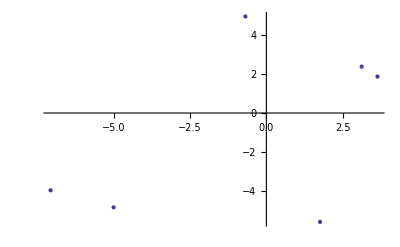

```mathematica
Partition[mds[[2,All,-1]],2] // ListPlot
```

```mathematica
ClearAll[drivetime,cities,pairs,times,matrix]
```

```mathematica
drivetime[{city1_String,city2_String}]:=Module[{test},
test=Import["https://maps.googleapis.com/maps/api/directions/json?origin="<>city1<>"&destination="<>city2<>"&sensor=false","JSON"];
Cases[test,HoldPattern["duration"->value_]:>value,Infinity][[1,2,2]]]
```

```mathematica
cities={"New_York","Los_Angeles","Chicago","Houston","Philadelphia","Phoenix","San_Antonio","San_Diego","Dallas","San_Jose"};
pairs=Tuples[cities,2]
```

{{New_York,New_York},{New_York,Los_Angeles},{New_York,Chicago},{New_York,Houston},{New_York,Philadelphia},{New_York,Phoenix},{New_York,San_Antonio},{New_York,San_Diego},{New_York,Dallas},{New_York,San_Jose},{Los_Angeles,New_York},{Los_Angeles,Los_Angeles},{Los_Angeles,Chicago},{Los_Angeles,Houston},{Los_Angeles,Philadelphia},{Los_Angeles,Phoenix},{Los_Angeles,San_Antonio},{Los_Angeles,San_Diego},{Los_Angeles,Dallas},{Los_Angeles,San_Jose},{Chicago,New_York},{Chicago,Los_Angeles},{Chicago,Chicago},{Chicago,Houston},{Chicago,Philadelphia},{Chicago,Phoenix},{Chicago,San_Antonio},{Chicago,San_Diego},{Chicago,Dallas},{Chicago,San_Jose},{Houston,New_York},{Houston,Los_Angeles},{Houston,Chicago},{Houston,Houston},{Houston,Philadelphia},{Houston,Phoenix},{Houston,San_Antonio},{Houston,San_Diego},{Houston,Dallas},{Houston,San_Jose},{Philadelphia,New_York},{Philadelphia,Los_Angeles},{Philadelphia,Chicago},{Philadelphia,Houston},{Philadelphia,Philadelphia},{Philadelphia,Phoenix},{Philadelphia,San_Antonio},{Philadelphia,San_Diego},{Philadelphia,Dallas},{Philadelphia,San_Jose},{Phoenix,New_York},{Phoenix,Los_Angeles},{Phoenix,Chicago},{Phoenix,Houston},{Phoenix,Philadelphia},{Phoenix,Phoenix},{Phoenix,San_Antonio},{Phoenix,San_Diego},{Phoenix,Dallas},{Phoenix,San_Jose},{San_Antonio,New_York},{San_Antonio,Los_Angeles},{San_Antonio,Chicago},{San_Antonio,Houston},{San_Antonio,Philadelphia},{San_Antonio,Phoenix},{San_Antonio,San_Antonio},{San_Antonio,San_Diego},{San_Antonio,Dallas},{San_Antonio,San_Jose},{San_Diego,New_York},{San_Diego,Los_Angeles},{San_Diego,Chicago},{San_Diego,Houston},{San_Diego,Philadelphia},{San_Diego,Phoenix},{San_Diego,San_Antonio},{San_Diego,San_Diego},{San_Diego,Dallas},{San_Diego,San_Jose},{Dallas,New_York},{Dallas,Los_Angeles},{Dallas,Chicago},{Dallas,Houston},{Dallas,Philadelphia},{Dallas,Phoenix},{Dallas,San_Antonio},{Dallas,San_Diego},{Dallas,Dallas},{Dallas,San_Jose},{San_Jose,New_York},{San_Jose,Los_Angeles},{San_Jose,Chicago},{San_Jose,Houston},{San_Jose,Philadelphia},{San_Jose,Phoenix},{San_Jose,San_Antonio},{San_Jose,San_Diego},{San_Jose,Dallas},{San_Jose,San_Jose}}

```mathematica
drivetime[{pairs[[2,1]],pairs[[2,2]]}]
```

145168

```mathematica
times=drivetime /@ pairs[[All]]
```

{0,145168,42874,85225,6041,128447,95255,146468,81571,154380,145259,0,103678,77929,141914,19253,68024,7045,72881,18056,43082,103458,0,58920,41163,92667,65358,106631,50632,112670,85342,77632,58800,0,81297,58720,10213,73201,12403,95123,6017,142276,41078,81116,0,124696,91146,142717,77462,152584,128338,19175,92344,58989,124359,0,49084,18377,53941,36666,95407,67865,65236,10239,91362,48953,0,63434,14906,85356,146247,7136,106851,73364,142268,18345,63459,0,68316,24986,81673,72690,50530,12376,77628,53778,14832,68259,0,88539,153760,18081,112179,95507,151841,36831,85602,25044,87787,0}

```mathematica
matrix=Partition[times,10]
```

{{0,145168,42874,85225,6041,128447,95255,146468,81571,154380},{145259,0,103678,77929,141914,19253,68024,7045,72881,18056},{43082,103458,0,58920,41163,92667,65358,106631,50632,112670},{85342,77632,58800,0,81297,58720,10213,73201,12403,95123},{6017,142276,41078,81116,0,124696,91146,142717,77462,152584},{128338,19175,92344,58989,124359,0,49084,18377,53941,36666},{95407,67865,65236,10239,91362,48953,0,63434,14906,85356},{146247,7136,106851,73364,142268,18345,63459,0,68316,24986},{81673,72690,50530,12376,77628,53778,14832,68259,0,88539},{153760,18081,112179,95507,151841,36831,85602,25044,87787,0}}

{Point[{-59540.6,-62766.3}],Point[{51473.9,30603.4}],Point[{-21806.6,-43852.7}],Point[{-24818.,15622.5}],Point[{-60396.2,-57092.5}],Point[{32239.3,28284.7}],Point[{-15966.,21723.3}],Point[{46658.1,36774.7}],Point[{-16758.1,6709.5}],Point[{68917.6,24105.8}]}

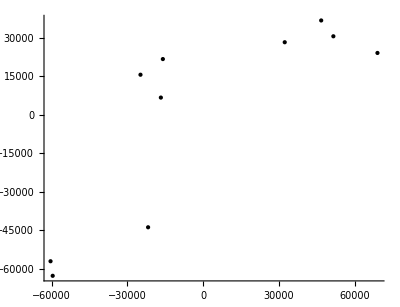

```mathematica
mudisc[mat_,dims_]:=Module[{leng,x,stress,temp},
leng=mat //Length;
stress=Sum[(Norm[Table[x[i,k],{k,dims}]-Table[x[j,k],{k,dims}]]-mat[[i,j]])^2,{i,leng},{j,i,leng}];
temp=NMinimize[stress,Table[x[i,k],{i,leng},{k,dims}]//Flatten];
Partition[temp[[2,All,-1]],2]
]
grp=Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{cities,mudisc[matrix,2]}]
Graphics[grp, Axes->True]
```